```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Elastic Collisions in Lab Frame

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

#### Second solution is physical one

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

```mathematica
etransfer=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

```mathematica
1/(2Pi)Integrate[etransfer,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

#### Proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei

```mathematica
ζ=M^2/(m+M)^2;
```

#### How many elastic collisions before lose O(1) of energy?

```mathematica
Solve[ζ^c==0.5/.{M->12000,m->100},c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→41.7619}}

```mathematica
Solve[ζ^c==0.1/.{M->12000,m->1000},c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→14.3835}}

```mathematica
dedxelasticmeson=Piecewise[{{ϵ/(50/((n/Z)σ)),ϵ≤10},{0,ϵ>10}}];
dedxelasticnucleon=Piecewise[{{ϵ/(10/((n/Z)σ)),ϵ≤10},{0,ϵ>10}}];
dedxnonelastic=Piecewise[{{ϵ (n/Z σ),ϵ>10},{0,ϵ≤10}}];
```

#### In units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^4 Barn(200 Mega ElectronVolt Fermi)^-2,(Mega ElectronVolt)^2]//N
```

0.0025 ElectronVolt^2 Mega^2

```mathematica
Convert[ElectronVolt^2 Mega^2*(200 Mega ElectronVolt*Fermi)^-1,Mega ElectronVolt/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

#### Elastic and Nonelastic stopping powers (σ in barns)

```mathematica
nucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,10^-1,10^10},PlotLegends->{"Nuclear Inelastic"},PlotStyle->{Purple,Thick}];
meson=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,10^-1,10^10},PlotLegends->{"Nuclear Inelastic"},PlotStyle->{Purple,Thick}];
elasticnucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxelasticnucleon,{n->8,Z->6}],{σ->1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,1,10^10},PlotLegends->{"Nuclear Elastic"},PlotStyle->{Cyan,Thick}];
elasticmeson=LogLogPlot[ReplaceAll[ReplaceAll[dedxelasticmeson,{n->8,Z->6}],{σ->1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,1,10^10},PlotLegends->{"Nuclear Elastic"},PlotStyle->{Cyan,Thick}];
nucleon2=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->0.008,Z->6}],{σ->0.1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,10^-1,10^10},PlotLegends->{"Nuclear Inelastic"},PlotStyle->{Purple,Thick}];
meson2=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->0.008,Z->6}],{σ->0.1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,10^-1,10^10},PlotLegends->{"Nuclear Inelastic"},PlotStyle->{Purple,Thick}];
elasticnucleon2=LogLogPlot[ReplaceAll[ReplaceAll[dedxelasticnucleon,{n->0.008,Z->6}],{σ->1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,1,10^10},PlotLegends->{"Nuclear Elastic"},PlotStyle->{Cyan,Thick}];
elasticmeson2=LogLogPlot[ReplaceAll[ReplaceAll[dedxelasticmeson,{n->0.008,Z->6}],{σ->1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,1,10^10},PlotLegends->{"Nuclear Elastic"},PlotStyle->{Cyan,Thick}];
```

#### Canvases for stopping power plots

```mathematica
canvasphoton=LogLogPlot[10^20,{ϵ,1,10^8},Frame->True,PlotRange->{1,10^7},FrameLabel->{"Photon Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvasphoton2=LogLogPlot[10^20,{ϵ,1,10^8},Frame->True,PlotRange->{10^-4,10^4},FrameLabel->{"Photon Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvasnucleon=LogLogPlot[10^20,{ϵ,1,10^7},Frame->True,PlotRange->{1,10^7},FrameLabel->{"Nucleon Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvasnucleon2=LogLogPlot[10^20,{ϵ,1,10^7},Frame->True,PlotRange->{10^-4,10^4},FrameLabel->{"Nucleon Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvaspion=LogLogPlot[10^20,{ϵ,1,10^7},Frame->True,PlotRange->{1,10^9},FrameLabel->{"Pion Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvaspion2=LogLogPlot[10^20,{ϵ,1,10^7},Frame->True,PlotRange->{10^-4,10^4},FrameLabel->{"Pion Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvaselectron=LogLogPlot[10^20,{ϵ,1,10^8},Frame->True,PlotRange->{10^-3,10^7},FrameLabel->{"Electron Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
canvaselectron2=LogLogPlot[10^20,{ϵ,1,10^8},Frame->True,PlotRange->{10^-5,10^5},FrameLabel->{"Electron Energy (MeV)","Stopping Power (MeV/10^-5cm)"},LabelStyle-> Directive[Bold]];
```

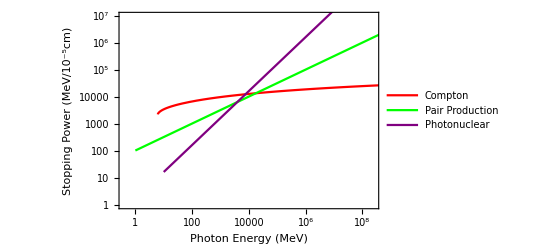

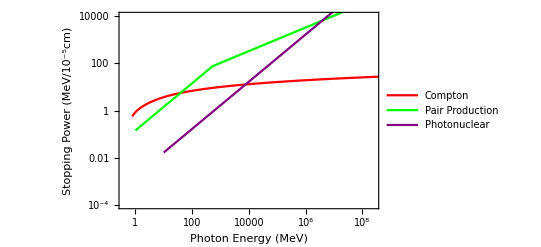

```mathematica
photonall=Show[canvasphoton,compton,photonpp,photonhad]
photonall2=Show[canvasphoton2,compton2,photonpp2,photonhad2]
```

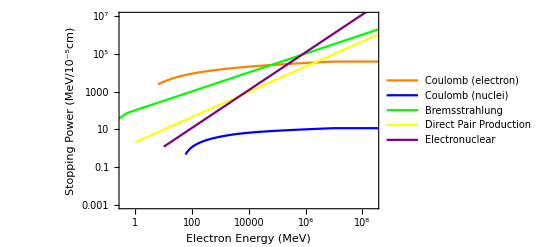

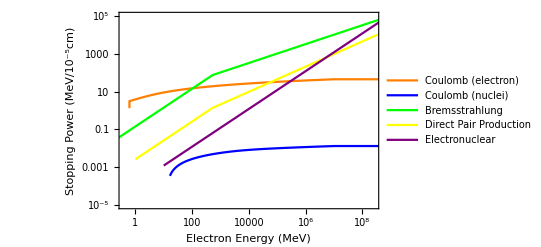

```mathematica
electronall=Show[canvaselectron,electronpauli,electronpauliflat,electron,electronflat,electronbrem,electrondpp,electronhad]
electronall2=Show[canvaselectron2,electronpauli2,electronpauliflat2,electron2,electronflat2,electronbrem2,electrondpp2,electronhad2]
```

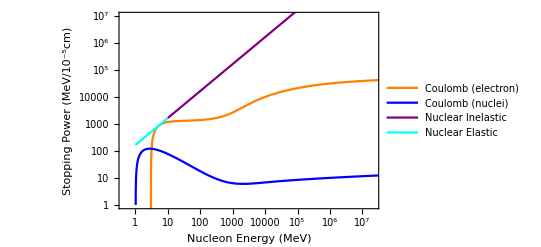

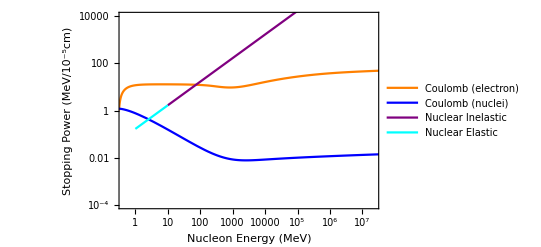

```mathematica
nucleonall=Show[canvasnucleon,protonpauli,proton,nucleon,elasticnucleon]
nucleonall2=Show[canvasnucleon2,protonpauli2,proton2,nucleon2,elasticnucleon2]
```

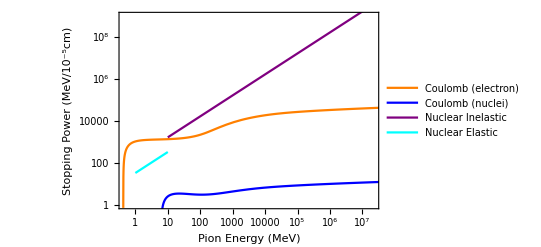

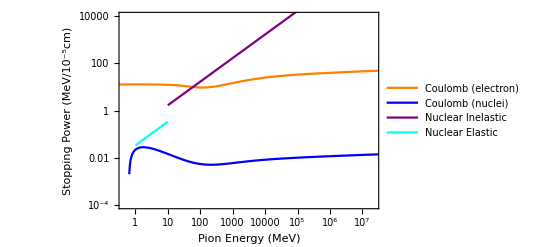

```mathematica
pionall=Show[canvaspion,pionpauli,pion,meson,elasticmeson]
pionall2=Show[canvaspion2,pionpauli2,pion2,meson2,elasticmeson2]
```

```mathematica
Export["/Users/NewUser/Documents/Qballs/SPphoton.pdf",photonall];
Export["/Users/NewUser/Documents/Qballs/SPelectron.pdf",electronall];
Export["/Users/NewUser/Documents/Qballs/SPpion.pdf",pionall];
Export["/Users/NewUser/Documents/Qballs/SPnucleon.pdf",nucleonall];
Export["/Users/NewUser/Documents/Qballs/SPphoton2.pdf",photonall2];
Export["/Users/NewUser/Documents/Qballs/SPelectron2.pdf",electronall2];
Export["/Users/NewUser/Documents/Qballs/SPpion2.pdf",pionall2];
Export["/Users/NewUser/Documents/Qballs/SPnucleon2.pdf",nucleonall2];
```

#### $$$$$$$$$$$$$

```mathematica
Xhad=Convert[1/(n σinel)Log[ϵ/10]/.{n->10^32 Centimeter^-3,σinel->0.1Barn},Centimeter];
λel=Convert[1/(n*σ)*Sqrt[10]/.{n->10^32 Centimeter^-3,σ->1Barn},Centimeter];
```

```mathematica
{Xhad,λel}/.ϵ->10^6//N
```

{1.15129×10^-6 Centimeter,3.16228×10^-8 Centimeter}

#### Electrons and Photons

```mathematica
Integrate[((√(Elpm/ϵ) ϵ)/X0)^-1,{ϵ,ϵc,ϵ},Assumptions->{ϵ>0,ϵc>0}]
```

ConditionalExpression[(2 X0 (√ϵ-√ϵc))/(√Elpm),ϵ>ϵc]

```mathematica
FullSimplify[(2 X0 (√ϵ))/(√Elpm)/.{Elpm->(me^2 X0 α)/(4Pi)}/.X0->((4n Z^2 α^3)/me^2)^-1,Assumptions->{me>0,n>0,Z>0,α>0,ϵ>0}]
```

(2 √π √(ϵ/n))/(Z α^2)

```mathematica
Xem=Convert[(2 √π √(ϵ/n))/(Z α^2)*(200 Mega ElectronVolt*Fermi)/.{Z->6,α->1/137,n->0.8(Mega ElectronVolt)^3,ϵ->ϵ Mega ElectronVolt},Centimeter]
```

2.47959×10^-7 Centimeter √ϵ